## Analysis of Antigen output

## Basic parameters

```mathematica
demeCount=3;
```

```mathematica
demes={"North","Tropics","South"};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/SimTree

```mathematica
spatialColors={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

```mathematica
spatialColors=Map[Lighter[#,0.1]&,spatialColors]
```

{RGBColor[0.7885,0.7552,0.3466],RGBColor[0.3916,0.6481,0.7372],RGBColor[0.8713,0.2179,0.2188]}

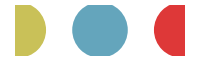

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,spatialColors]},PlotRange->All,AspectRatio->0.3,ImageSize->200]
```

```mathematica
spatialColorRules=MapIndexed[#2[[1]]-1->#1&,spatialColors];
```

```mathematica
trunkColors={GrayLevel[0.3],RGBColor[0.857,0.131,0.132]};
```

```mathematica
trunkColorRules=MapIndexed[#2[[1]]-1->#1&,trunkColors];
```

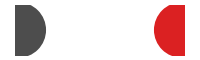

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,trunkColors]},PlotRange->All,AspectRatio->0.3,ImageSize->200]
```

k=11, mod=8 for H3N2

k=4, mod=1 for H1N1

```mathematica
k=11;
```

```mathematica
mod=8;
```

```mathematica
clusterColors=Table[Lighter[ColorData["Rainbow"][FractionalPart[i-0.001]],0.1],{i,1/k,mod,mod/k}];
```

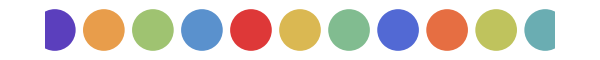

```mathematica
Graphics[{PointSize[0.05],MapIndexed[{#1,Point[{#2[[1]],0}]}&,clusterColors]},PlotRange->All,AspectRatio->0.1,ImageSize->600]
```

```mathematica
narrowWidth=255;
```

```mathematica
extraNarrowWidth=215;
```

```mathematica
padding={{35,5},{20,15}};
```

```mathematica
fullPadding={{37,2},{29,5}};
```

```mathematica
partialPadding={{15,2},{13,2}};
```

## Loess fit

```mathematica
LoessFit[(x_)?VectorQ,data_,α_:0.75,λ_:1]:=Table[LoessFit[x[[i]],data,α,λ],{i,Length[x]}]
```

```mathematica
LoessFit[(x_)?NumberQ,data_,α_:0.75,λ_:1]:=WLSFit[data,LoessWts[x,data,α],λ,x];
```

```mathematica
WLSFit[data_,wts_,ldegree_:1,x_]:=Fit[Transpose[(wts*#1&)/@Join[{Table[1,{Length[data]}]},Transpose[data]]],Join[{u},Table[v^i,{i,ldegree}]],{u,v}]/.{u->1,v->x}
```

```mathematica
LoessWts[x_,data_,α_]:=Tricube[(x-First[Transpose[data]])/LoessDistance[x,data,α]]
```

```mathematica
Tricube=Compile[{{x,_Real,1}},If[Abs[#]<1,(1-Abs[#]^3)^3,0]&/@x];
```

```mathematica
LoessDistance[x_,data_,α_]:=Module[{A=Max[1,α],X=First[Transpose[data]],q},q=Min[Length[X],Ceiling[α*Length[X]]];A*Sort[Abs[X-x]][[q]]]
```

## Options (white)

```mathematica
SetOptions[Plot,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->White,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->White,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->White,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->White,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListContourPlot,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->White,ImageSize->600];
```

```mathematica
SetOptions[ContourPlot,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->White,ImageSize->600];
```

```mathematica
SetOptions[DiscretePlot,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,FrameStyle->White,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->White,ImageSize->600,FrameStyle->White,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->White,FrameStyle->White,ImageSize->600,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[White,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->White,FrameStyle->White,ImageSize->600,PlotRange->{0,All}];
```

## Options (black)

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->600];
```

```mathematica
SetOptions[ContourPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->600];
```

```mathematica
SetOptions[DiscretePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->600,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->600,PlotRange->{0,All},ChartStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

## World-wide SIR

Assuming weekly output

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0192

```mathematica
endTime=data[[-1,1]]
```

39.9863

```mathematica
popSize=data[[1,3]]
```

90000000

### Prevalence

```mathematica
N[Mean[data[[All,5]]]]
```

75918.1

```mathematica
N[HarmonicMean[data[[All,5]]]]
```

4289.43

```mathematica
prev=Transpose[{data[[All,1]],(data[[All,5]]*100000)/popSize}];
```

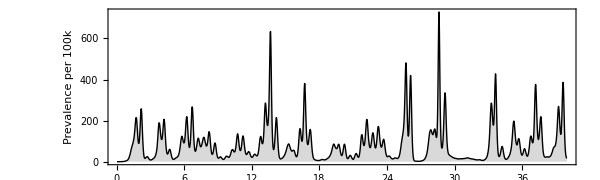

```mathematica
fig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"","Prevalence per 100k"},ImagePadding->{{40,10},{15,5}}]
```

```mathematica
Export["prevalence.pdf",fig,"PDF"]
```

prevalence.pdf

### Incidence

```mathematica
inc=Transpose[{data[[All,1]],(data[[All,7]]*100000)/popSize}];
```

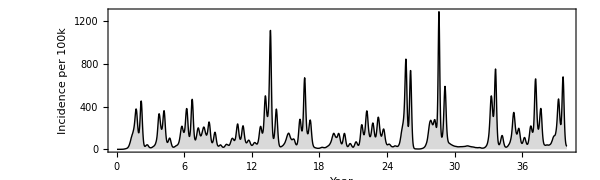

```mathematica
fig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->LightGray,FrameLabel->{"Year","Incidence per 100k"}]
```

```mathematica
Export["incidence.pdf",fig,"PDF"]
```

incidence.pdf

### Yearly incidence

Mean incidence per year

```mathematica
inc=data[[All,{1,7}]];
```

```mathematica
attackRates=N[Table[Total[Select[inc,(#[[1]]>i&&#[[1]]≤i+1)&][[All,2]]]/popSize,{i,0,39}]]
```

{0.00177312,0.0934167,0.067681,0.0666705,0.0754611,0.0495611,0.132228,0.0839386,0.0677854,0.0178723,0.0622741,0.0542795,0.0530457,0.230973,0.0622203,0.0522396,0.143045,0.0456067,0.0127524,0.0591944,0.0333751,0.0525826,0.107029,0.0870588,0.017525,0.163671,0.07686,0.0566857,0.201059,0.0896845,0.0135292,0.0127818,0.0120334,0.177954,0.0326849,0.0956853,0.0609284,0.154582,0.0368502,0.163411}

```mathematica
N[(Total[inc[[All,2]]]/endTime)]
```

6.92785×10^6

```mathematica
meaninc=N[(Total[inc[[All,2]]]/endTime)/popSize]
```

0.0769761

Flu incidence is 10% per year and prevalence is 0.14%.

### Diversity

```mathematica
div=data[[All,{1,2}]];
```

```mathematica
meandiv=Mean[div][[2]]
```

3.89937

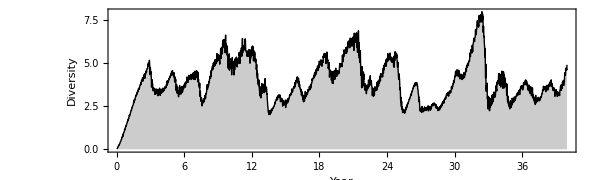

```mathematica
fig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"Year","Diversity"}]
```

```mathematica
Export["diversity.pdf",fig,"PDF"]
```

diversity.pdf

## Regional SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases
18 | southN
19 | southS
20 | southI
21 | southR
22 | southCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0192

```mathematica
endTime=data[[-1,1]]
```

39.9863

```mathematica
demePopSize=Mean[Mean[data[[All,8;;-1;;5]]]]
```

30000000

### Yearly incidence

```mathematica
incList=Table[data[[All,i]],{i,12,12+(demeCount-1)*5,5}];
```

```mathematica
TableForm[N[Map[Total[#]&,incList]]/(endTime-startTime),TableHeadings->{demes}]
```

North | 2.23057×10^6
Tropics | 2.37185×10^6
South | 2.32876×10^6

```mathematica
{meanIncNorth,meanIncTropics,meanIncSouth}=Map[Total[#]&,incList]/((endTime-startTime)*(popSize/demeCount));
```

```mathematica
TableForm[Round[{meanIncNorth,meanIncTropics,meanIncSouth},0.001],TableHeadings->{demes}]
```

North | 0.074
Tropics | 0.079
South | 0.078

### Yearly attack rates

```mathematica
step=1;
```

```mathematica
attackRateList=Table[Table[{j+0.5,Total[Select[data,(#[[1]]≥j&&#[[1]]<j+step&)][[All,i]]]/(popSize/demeCount)},{j,Floor[startTime],Ceiling[endTime],step}],{i,12,12+(demeCount-1)*5,5}];
```

```mathematica
attackRateList=Join[{Table[{j,Total[Select[data,(#[[1]]≥j&&#[[1]]<j+step&)][[All,12]]]/(popSize/demeCount)},{j,Floor[startTime],Ceiling[endTime],step}]},Table[Table[{j+0.5,Total[Select[data,(#[[1]]≥j&&#[[1]]<j+step&)][[All,i]]]/(popSize/demeCount)},{j,Floor[startTime],Ceiling[endTime],step}],{i,17,12+(demeCount-1)*5,5}]];
```

```mathematica
Mean[N[attackRateList[[1]]]]
```

{20.,0.0724792}

```mathematica
Max[N[attackRateList[[1]]]]
```

40.

```mathematica
max=Ceiling[N[Max[Map[Max,attackRateList[[All,2]]]]],0.01]
```

1.5

```mathematica
max=0.25;
```

```mathematica
Mean[N[attackRateList[[1,All,2]]]]
```

0.0724792

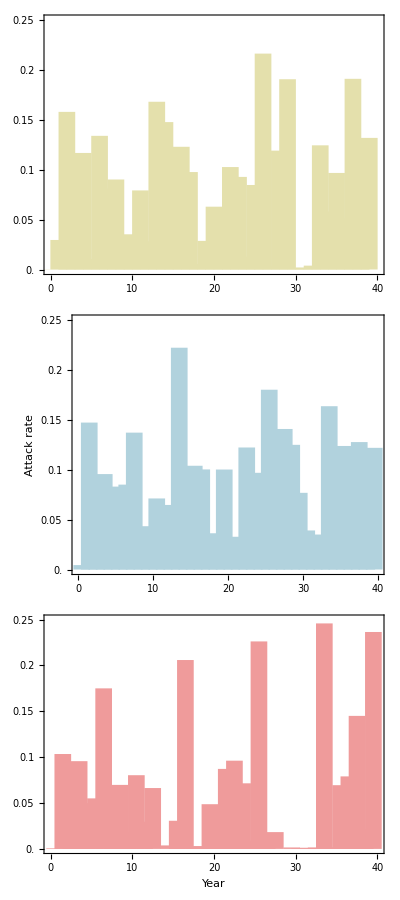

```mathematica
fig=Grid[Table[{ListPlot[attackRateList[[i]],PlotRange->{{0,40},{0,max}},AspectRatio->0.2,Filling->Axis,PlotStyle->None,FillingStyle->Directive[Thickness[0.02],CapForm[None],Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Attack rate",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}},FrameTicks->{{Table[{i,ToString[i],{0,0.005}},{i,0,0.30,0.05}],None},{Table[{i,ToString[i],{0,0.005}},{i,0,40,5}],None}}]},{i,demeCount}]]
```

```mathematica
Export["attackRateSpatial.pdf",fig,"PDF"]
```

attackRateSpatial.pdf

### Prevalence

```mathematica
prevList=Table[Transpose[{data[[All,1]],data[[All,i]]*100000/demePopSize}],{i,10,10+(demeCount-1)*5,5}];
```

```mathematica
max=N[Max[Map[Max,prevList]]]
```

2058.22

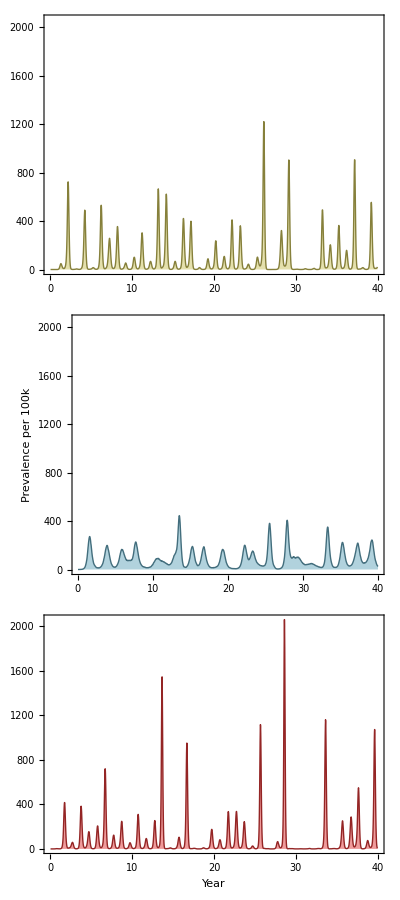

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Prevalence per 100k",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}}]},{i,demeCount}]]
```

```mathematica
Export["prevalenceSpatial.pdf",fig,"PDF"]
```

prevalenceSpatial.pdf

### Incidence - spatial

```mathematica
incList=Table[Transpose[{data[[All,1]],data[[All,i]]*100000/demePopSize}],{i,12,12+(demeCount-1)*5,5}];
```

```mathematica
max=N[Max[Map[Max,incList]]]
```

3646.78

```mathematica
max=1500
```

1500

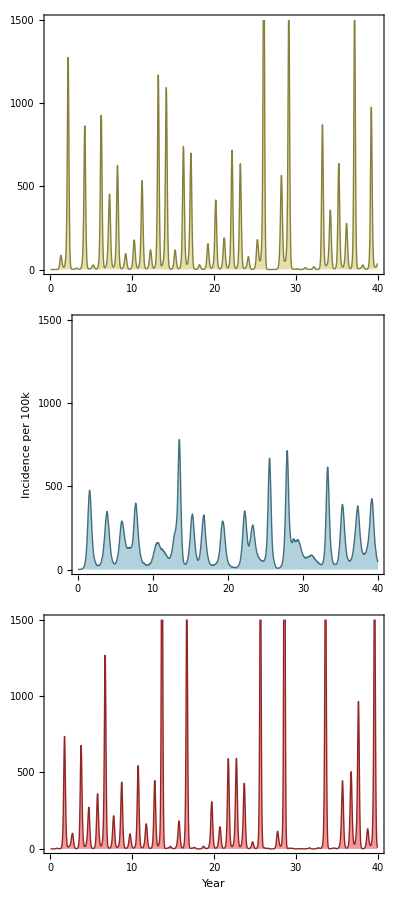

```mathematica
fig=Grid[Table[{ListLinePlot[incList[[i]],PlotRange->{0,max},AspectRatio->0.2,Filling->Axis,PlotStyle->Darker[spatialColors[[i]]],FillingStyle->Directive[Lighter[spatialColors[[i]],0.5]],FrameLabel->{If[i==demeCount,"Year",""],If[i==2,"Incidence per 100k",""]},ImagePadding->{{50,10},{If[i==demeCount,30,15],5}},FrameTicks->{{Table[{i,ToString[i],{0,0.005}},{i,0,1500,500}],None},{Table[{i,ToString[i],{0,0.005}},{i,0,40,5}],None}}]},{i,demeCount}]]
```

```mathematica
Export["incidenceSpatial.pdf",fig,"PDF"]
```

incidenceSpatial.pdf

## Tips

```mathematica
tipScale=0.0015;
```

```mathematica
tipData=Import["out.tips","CSV"];
```

```mathematica
traitHeader=tipData[[1]];
```

```mathematica
TableForm[traitHeader,TableHeadings->{Range[10]}]
```

1 | name
2 | year
3 | trunk
4 | tip
5 | mark
6 | location
7 | layout
8 | ag1
9 | ag2

```mathematica
tipData=Drop[tipData,1];
```

```mathematica
name=1;year=2;trunk=3;tip=4;mark=5;loc=6;layout=7;ag1=8;ag2=9;
```

### Flip

tipData = Map[{1, 1, 1, 1, 1, 1, 1, 1, -1}*# &, tipData];

### Rotate

```mathematica
rotate[point_, theta_] := With[{x = point[[1]], y = point[[2]]},
  {x Cos[theta] - y Sin[theta], x Sin[theta] + y Cos[theta]}
  ]
```

```mathematica
tipData = Map[Join[Take[#, 7], rotate[#[[{ag1, ag2}]], 0.7]] &, tipData];
```

### First tip

```mathematica
firstIndex=First[Ordering[tipData[[All,year]],1]]
```

2019

```mathematica
length=Length[tipData]
```

6044

### Graphics settings

```mathematica
frameWindow=1.0;
```

```mathematica
imageSize=600;
```

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-100,100,frameWindow}],{2},{2}];
```

### Map

```mathematica
noise[]:=With[{theta=RandomReal[{0,2Pi}],r=RandomVariate[ExponentialDistribution[1.9]]},
{r Cos[theta],r Sin[theta]}];
```

```mathematica
jitter=Map[#+noise[]&,tipData[[All,{ag1,ag2}]]];
```

```mathematica
plotRange={{Floor[Min[jitter[[All,1]]]],Ceiling[Max[jitter[[All,1]]]]},{Floor[Min[jitter[[All,2]]]],Ceiling[Max[jitter[[All,2]]]]}}
```

{{-7,42},{-3,25}}

```mathematica
avgDist[pointsA_,pointsB_]:=Mean[MapThread[EuclideanDistance,{RandomChoice[pointsA,1000],RandomChoice[pointsB,1000]}]]
```

```mathematica
clustered=FindClusters[jitter->Range[length],k,Method->{"Agglomerate","Linkage"->"Ward"},DistanceFunction->EuclideanDistance];
```

```mathematica
cluster[i_]:=jitter[[clustered[[i]]]]
```

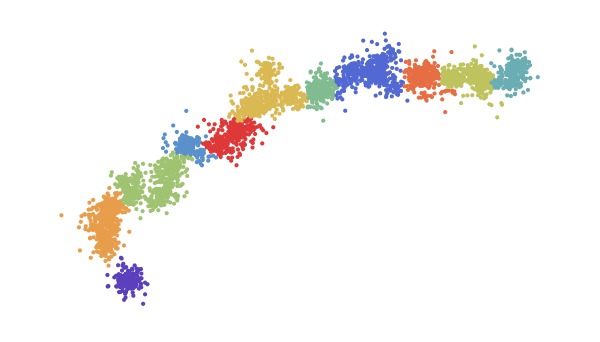

```mathematica
fig=ListPlot[Map[jitter[[#]]&,clustered],PlotStyle->clusterColors,AspectRatio->Automatic,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize]
```

```mathematica
Mean[Table[avgDist[cluster[i],cluster[i]],{i,k}]]
```

1.79939

```mathematica
Mean[Flatten[Table[Table[avgDist[cluster[i],cluster[j]],{j,i+1,k}],{i,k}]]]
```

19.2513

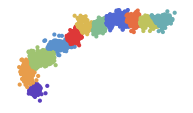

```mathematica
fig=ListPlot[Map[jitter[[#]]&,clustered],PlotStyle->Map[Directive[#,PointSize[Small]]&,clusterColors],AspectRatio->Automatic,PlotRange->plotRange,PlotRangePadding->0.05,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->Gray,Frame->False,ImageSize->extraNarrowWidth*0.9,ImagePadding->partialPadding]
```

```mathematica
Export["mapClusters.pdf",fig,"PDF"]
```

mapClusters.pdf

### Cluster function

```mathematica
clusterCenters=Map[Mean[jitter[[#]]]&,clustered]
```

{{0.243231,0.0380864},{-1.80376,5.61404},{2.88834,9.73939},{6.29607,13.3725},{10.6444,14.5287},{14.2088,18.3954},{19.4994,19.1741},{24.4841,20.8499},{29.7607,20.4282},{34.3826,20.2201},{38.8385,20.8604}}

```mathematica
clusterFunction[p_]:=First[Nearest[clusterCenters->Range[k],p]]
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#]]],Point[#]}&,jitter];
```

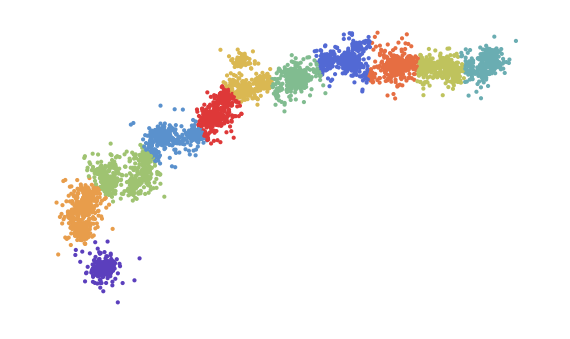

```mathematica
Graphics[points,AspectRatio->Automatic,PlotRange->plotRange,GridLines->{Range[-100,100,frameWindow],Range[-100,100,frameWindow]},GridLinesStyle->LightGray,Frame->False,ImageSize->imageSize*0.95]
```

### AG1 vs AG2

```mathematica
tipScale=0.0025;
```

```mathematica
tallies=Tally[tipData[[All,{ag1,ag2}]]];
```

```mathematica
tallies=Sort[tallies,#1[[2]]>#2[[2]]&];
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#[[1]]]]],Disk[#[[1]],N[0.05*Sqrt[#[[2]]]]]}&,tallies];
```

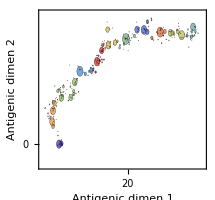

```mathematica
fig=Graphics[{EdgeForm[Thickness[0.0012]],Opacity[0.8],points},AspectRatio->Automatic,ImageSize->extraNarrowWidth,PlotRange->plotRange,FrameLabel->{"Antigenic dimen 1","Antigenic dimen 2"},Frame->{True,True,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,5}],None},{Table[{i,i,{0,0.005}},{i,-50,50,5}],None}},ImagePadding->fullPadding]
```

```mathematica
Export["tipsAG1AG2.pdf",fig,"PDF"]
```

tipsAG1AG2.pdf

### Distance from origin

```mathematica
dist[point_]:=EuclideanDistance[tipData[[firstIndex,{ag1,ag2}]],point]
```

```mathematica
list=Map[{#[[1]],dist[#[[{2,3}]]]}&,tipData[[All,{year,ag1,ag2}]]];
```

```mathematica
meanFluxRate=(Max[list[[All,2]]]-Min[list[[All,2]]])/(Max[tipData[[All,year]]]-Min[tipData[[All,year]]])
```

1.15402

```mathematica
points=Map[{clusterColors[[clusterFunction[#[[{2,3}]]]]],PointSize[Small],Point[{#[[1]],dist[#[[{2,3}]]]}]}&,tipData[[All,{year,ag1,ag2}]]];
```

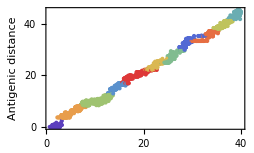

```mathematica
fig=Graphics[points,AspectRatio->0.6,ImageSize->narrowWidth,PlotRange->All,FrameLabel->{"Year","Antigenic distance"},Frame->{True,True,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,0,50,5}],None},{Table[{i,i,{0,0.005}},{i,0,50,5}],None}},ImagePadding->fullPadding]
```

```mathematica
Export["tipsYearDistance.pdf",fig,"PDF"]
```

tipsYearDistance.pdf

### Time series of incidence sorted by cluster

```mathematica
times=tipData[[All,year]];
```

```mathematica
step=N[(4*7)/365];
```

```mathematica
clusters=Map[times[[#]]&,clustered];
```

```mathematica
datelist=Table[i,{i,step,40,step}];
```

```mathematica
totalCounts=BinCounts[Flatten[clusters],{0,40,step}];
```

```mathematica
pro=Table[DeleteCases[N[MapThread[If[#2==0,Null,{#3,#1/#2}]&,{BinCounts[clusters[[i]],{0,40,step}],totalCounts,datelist}]],Null],{i,k}];
```

```mathematica
loess=Table[Map[{#,LoessFit[#,pro[[j]],0.05,1]}&,Table[i,{i,N[7/365],40,N[7/365]}]],{j,k}];
```

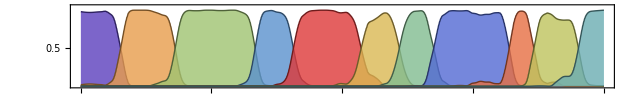

```mathematica
Show[Table[ListLinePlot[loess[[j]],Filling->Axis,FillingStyle->Directive[Opacity[0.8],clusterColors[[j]]],PlotStyle->Directive[Darker[clusterColors[[j]],0.5]],AspectRatio->0.15,Frame->{True,True,False,False},ImageSize->72*8.9,PlotRange->{0,1.05},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-0.5,1,0.25}],None},{Table[{i,i,{0,0.005}},{i,0,40,10}],None}}],{j,k}]]
```

```mathematica
minFrequency=0.1;
```

```mathematica
clusterEmergences[i_]:=With[{dates=loess[[i,All,1]][[Flatten[Position[loess[[i,All,2]],x_/;x>minFrequency]]]]},{Min[dates],Max[dates]}]
```

```mathematica
clusterDuration[i_]:=With[{dates=loess[[i,All,1]][[Flatten[Position[loess[[i,All,2]],x_/;x>minFrequency]]]]},Max[dates]-Min[dates]]
```

```mathematica
durations=Table[clusterDuration[i],{i,k}]
```

{3.49041,5.17808,7.13425,4.0274,6.94247,4.23836,3.83562,6.76986,2.89589,4.3726,3.31781}

```mathematica
Table[clusterEmergences[i],{i,k}]
```

{{0.0191781,3.50959},{2.53151,7.70959},{6.65479,13.789},{12.8301,16.8575},{15.6877,22.6301},{20.7507,24.989},{23.7041,27.5397},{26.4466,33.2164},{32.2575,35.1534},{34.1562,38.5288},{36.6685,39.9863}}

```mathematica
transitionTimes=MapThread[#1[[2]]-#2[[1]]&,{Table[clusterEmergences[i],{i,1,k-1}],Table[clusterEmergences[i],{i,2,k}]}]
```

{0.978082,1.05479,0.958904,1.16986,1.87945,1.28493,1.09315,0.958904,0.99726,1.86027}

```mathematica
incFig[deme_]:=Show[Table[ListLinePlot[MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{incList[[deme]],loess[[j]]}],Filling->Axis,FillingStyle->Directive[Opacity[0.8],clusterColors[[j]]],PlotStyle->Directive[Darker[clusterColors[[j]],0.5]],AspectRatio->0.15,Frame->{True,True,False,False},ImageSize->72*4.8,PlotRange->{0,1500},FrameTicks->{{Table[{i,i,{0,0.005}},{i,0,1500,500}],None},{Table[{i,i,{0,0.005}},{i,0,40,5}],None}}],{j,k}]]
```

```mathematica
incFig[deme_,max_,baseline_]:=Show[Table[ListLinePlot[MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{incList[[deme]],loess[[j]]}],Filling->Axis,FillingStyle->Directive[Opacity[0.8],clusterColors[[j]]],PlotStyle->Directive[Darker[clusterColors[[j]],0.5]],AspectRatio->0.15*N[max/baseline],Frame->{True,True,False,False},ImageSize->narrowWidth,PlotRange->{0,max},FrameTicks->{{Table[{i,i,{0,0.005}},{i,0,5000,500}],None},{Table[{i,i,{0,0.005}},{i,0,40,5}],None}}],{j,k}],ImagePadding->{{35,5},{20,15}}]
```

```mathematica
incFig[deme_,max_,baseline_]:=Show[Table[ListLinePlot[MapThread[{#1[[1]],#1[[2]]*#2[[2]]}&,{incList[[deme]],loess[[j]]}],Filling->Axis,FillingStyle->Directive[Opacity[0.8],clusterColors[[j]]],PlotStyle->Directive[Darker[clusterColors[[j]],0.5]],AspectRatio->0.2*N[max/baseline],Frame->{True,True,False,False},ImageSize->narrowWidth,PlotRange->{0,max},FrameTicks->{{Table[{i,i,{0,0.005}},{i,0,5000,500}],None},{Table[{i,i,{0,0.005}},{i,0,40,5}],None}}],{j,k}],ImagePadding->fullPadding]
```

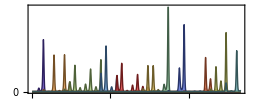

```mathematica
northInc=incFig[1,2000,1000]
```

```mathematica
Export["incidenceClustersNorth.pdf",northInc,"PDF"]
```

incidenceClustersNorth.pdf

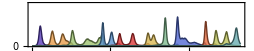

```mathematica
tropicsInc=incFig[2,1000,1000]
```

```mathematica
Export["incidenceClustersTropics.pdf",tropicsInc,"PDF"]
```

incidenceClustersTropics.pdf

```mathematica
southInc=incFig[3,2000,1000];
```

```mathematica
Export["incidenceClustersSouth.pdf",southInc,"PDF"]
```

incidenceClustersSouth.pdf

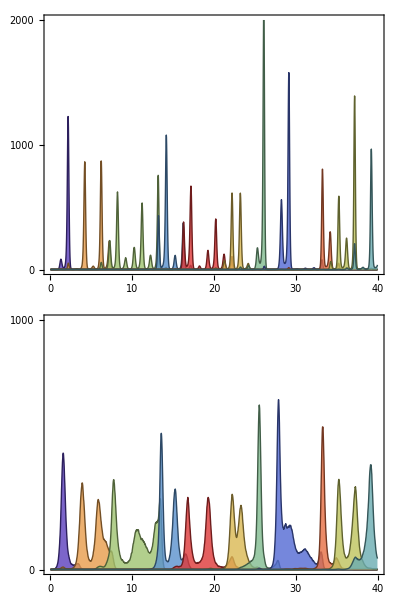

```mathematica
fig=Grid[{{northInc},{tropicsInc}}]
```

```mathematica
Export["incidenceClustersSpatial.pdf",fig,"PDF"]
```

incidenceClustersSpatial.pdf

```mathematica
totals=Accumulate[Join[{Table[0,{Length[Table[i,{i,N[7/365],40,N[7/365]}]]}]},Reverse[loess[[All,All,2]]]]];
```

```mathematica
totals=MapIndexed[{#2[[2]]*N[(7/365)],#1}&,totals,{2}];
```

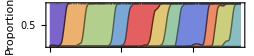

```mathematica
fig=ListLinePlot[totals,Filling ->Table[i->{{i+1},Directive[Opacity[0.8],clusterColors[[k+1-i]]]},{i,k}],PlotStyle->Table[Directive[Darker[clusterColors[[k+1-i]],0.5]],{i,k}],ImageSize->narrowWidth,AspectRatio->0.22,FrameTicks->{{Table[{i,i,{0,0.005}},{i,-0.5,1,0.5}],None},{Table[{i,i,{0,0.005}},{i,0,40,5}],None}},PlotRange->{0,1},FrameLabel->{"Year","Proportion"},ImagePadding->fullPadding]
```

```mathematica
Export["clusterTurnover.pdf",fig,"PDF"]
```

clusterTurnover.pdf

## Trees

First node is child, second is parent

```mathematica
branchScale=0.001;tipScale=0.0015;clip=0.005;
```

```mathematica
getThickness[count_]:=Thickness[Clip[branchScale*N[Sqrt[count]],{0,clip}]]
```

```mathematica
getPointSize[count_]:=PointSize[N[tipScale*Sqrt[count]]];
```

```mathematica
name=1;year=2;trunk=3;tip=4;mark=5;loc=6;layout=7;ag1=8;ag2=9;
```

```mathematica
branchData=ToExpression[Import["out.branches","Table"]];
```

```mathematica
branchData[[1]]
```

{{7ad81784,0.1973,0,0,1,1,15.8464,0.,0.},{4d20a47e,0.,1,0,1,0,130.27,0.,0.},6044}

```mathematica
branchData[[1,{1,2},{year,layout}]]
```

{{0.1973,15.8464},{0.,130.27}}

### Flip

branchData = Map[{{1, 1, 1, 1, 1, 1, 1, 1, -1}*#[[1]], {1, 1, 1, 1, 1, 1, 1, 1, -1}*#[[2]], #[[3]]} &, branchData];

### Rotate

```mathematica
rotate[point_, theta_] := With[{x = point[[1]], y = point[[2]]},
  {x Cos[theta] - y Sin[theta], x Sin[theta] + y Cos[theta]}
  ]
```

```mathematica
branchData = Map[{Join[#[[1,1;;7]], rotate[#[[1,{ag1, ag2}]], 0.95]], Join[#[[2,1;;7]], rotate[#[[2,{ag1, ag2}]], 0.95]], #[[3]]} &, branchData];
```

### Reduction

```mathematica
slimBranches=Select[branchData,(#[[1,mark]]==1&&#[[2,mark]]==1&)];
```

```mathematica
Length[slimBranches]
```

15985

```mathematica
Length[Select[slimBranches,(#[[1,tip]]==1&)]]
```

378

### Time vs Layout - clusters

```mathematica
branchLines=Map[{Thickness[0.003],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

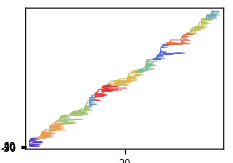

```mathematica
fig=Graphics[branchLines,AspectRatio->0.7,PlotRange->All,ImageSize->narrowWidth*0.915,FrameLabel->{"Year"},Frame->{True,False,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,5}],None},{Table[{i,i,{0,0.005}},{i,-50,50,5}],None}},ImagePadding->partialPadding]
```

```mathematica
Export["treeClusters.pdf",fig,"PDF"]
```

treeClusters.pdf

### Time vs Layout with location

```mathematica
branchLines=Map[{Thickness[0.0035],#[[1,loc]]/.spatialColorRules,Line[{#[[1,{year,layout}]],{#[[2,year]],#[[1,layout]]},#[[2,{year,layout}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

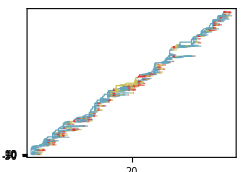

```mathematica
fig=Graphics[branchLines,AspectRatio->0.7,PlotRange->All,ImageSize->narrowWidth,FrameLabel->{"Year"},Frame->{True,False,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,5}],None},{Table[{i,i,{0,0.005}},{i,-50,50,5}],None}},ImagePadding->partialPadding]
```

```mathematica
Export["treeSpatial.pdf",fig,"PDF"]
```

$Aborted

### Time vs AG1 - clusters

```mathematica
mutBranches=Select[branchData,(EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001&)];
```

```mathematica
branchLines1=Map[{Thickness[0.0025],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{year,ag1}]],#[[2,{year,ag1}]]}]}&,mutBranches];
```

```mathematica
branchLines2=Map[{Thickness[0.0025],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{year,ag1}]],#[[2,{year,ag1}]]}]}&,slimBranches];
```

```mathematica
branchLines={CapForm["Round"],Join[branchLines1,branchLines2]};
```

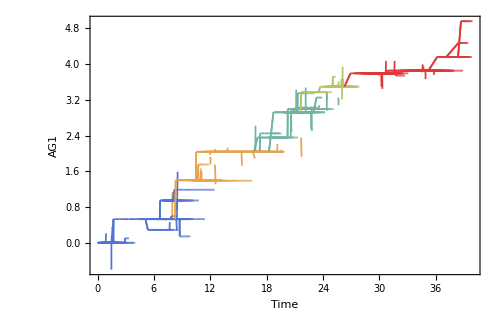

```mathematica
fig=Graphics[branchLines,AspectRatio->0.65,PlotRange->All,ImageSize->500,FrameLabel->{"Time","AG1"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeYearAG1Clusters.pdf",fig,"PDF"]
```

treeYearAG1Clusters.pdf

### AG1 vs AG2

```mathematica
mutBranches=Select[branchData,(EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001&)];
```

```mathematica
trunkPhenotypes=Union[Select[branchData,#[[1,trunk]]==1&][[All,1,{ag1,ag2}]]];
```

```mathematica
Length[mutBranches]
```

85

```mathematica
branchLines=Map[{getThickness[#[[3]]],#[[1,trunk]]/.trunkColorRules,Line[{#[[1,{ag1,ag2}]],Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}],#[[2,trunk]]/.trunkColorRules,Line[{Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}],#[[2,{ag1,ag2}]]}]}&,mutBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipBranches=Select[branchData,(#[[1,tip]]==1&)];
```

```mathematica
tallies=Tally[tipBranches[[All,1,{ag1,ag2}]]];
```

```mathematica
tallies=Sort[tallies,#1[[2]]>#2[[2]]&];
```

```mathematica
tipPoints=Map[{If[MemberQ[trunkPhenotypes,#[[1]]],trunkColors[[2]],trunkColors[[1]]],Disk[#[[1]],N[0.05*Sqrt[#[[2]]]]]}&,tallies];
```

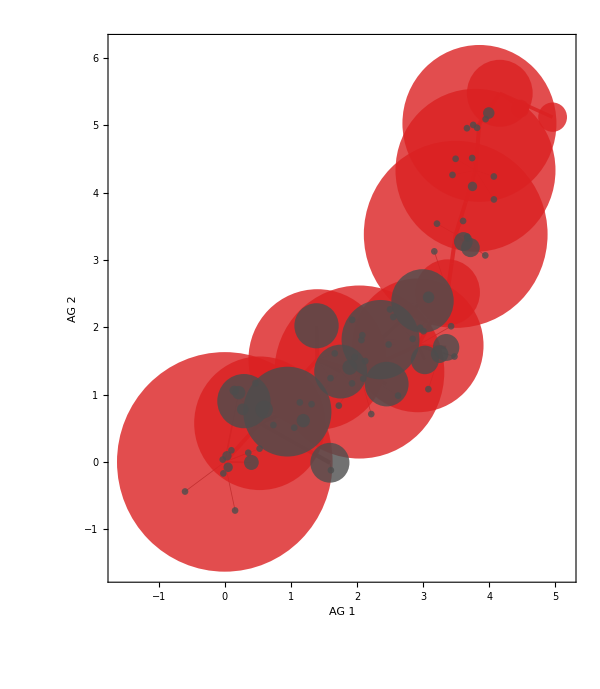

```mathematica
fig=Graphics[{Opacity[0.8],branchLines,tipPoints},AspectRatio->Automatic,PlotRange->All,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False}]
```

```mathematica
Export["treeAG1AG2.pdf",fig,"PDF"]
```

treeAG1AG2.pdf

### AG1 vs AG2 with clusters

```mathematica
mutBranches=Select[branchData,(EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001&)];
```

```mathematica
branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}],clusterColors[[clusterFunction[#[[2,{ag1,ag2}]]]]],Line[{Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}],#[[2,{ag1,ag2}]]}]}&,mutBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
tipBranches=Select[branchData,(#[[1,tip]]==1&)];
```

```mathematica
tallies=Tally[tipBranches[[All,1,{ag1,ag2}]]];
```

```mathematica
tipPoints=Map[{clusterColors[[clusterFunction[#[[1]]]]],Disk[#[[1]],N[0.05*Sqrt[#[[2]]]]]}&,tallies];
```

```mathematica
28*12
```

336

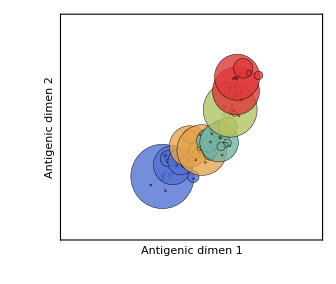

```mathematica
agtree=Graphics[{EdgeForm[Thickness[0.0012]],Opacity[0.8],branchLines,tipPoints},AspectRatio->Automatic,PlotRange->plotRange,ImageSize->336,Frame->{True,True,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,5}],None},{Table[{i,i,{0,0.005}},{i,-50,50,5}],None}},FrameLabel->{"Antigenic dimen 1","Antigenic dimen 2"}]
```

```mathematica
Export["treeAG1AG2Clusters.pdf",fig,"PDF"]
```

treeAG1AG2Clusters.pdf

## Host immunity

```mathematica
kern={{1,1,1},{1,1,1},{1,1,1}};
```

```mathematica
kern=kern/(3*Total[kern])
```

{{1/9,1/9,1/9},{1/9,1/9,1/9},{1/9,1/9,1/9}}

```mathematica
data=Import["out.immunity","CSV"];
```

```mathematica
Dimensions[data]
```

{133,84}

```mathematica
data=ListConvolve[kern,data];
```

```mathematica
Dimensions[data]
```

{131,82}

Flipping

data = Map[Reverse, data];

```mathematica
plotRange=Partition[Flatten[Import["out.range","CSV"]],2][[{1,2}]]
```

{{-11.,55.},{-21.,20.}}

```mathematica
plotRange=plotRange+{{1,-1},{1,-1}}
```

{{-10.,54.},{-20.,19.}}

Flipping

plotRange = {plotRange[[1]], Reverse[-1*plotRange[[2]]]}

{{-11., 57.}, {-13., 27.}}

```mathematica
interpolation=ListInterpolation[data,plotRange]
```

InterpolatingFunction[{{-10.,54.},{-20.,19.}},<>]

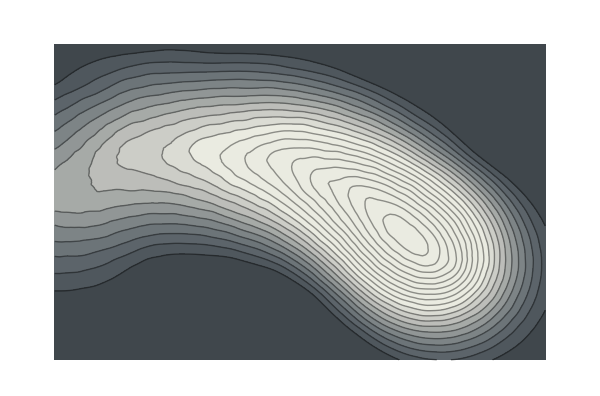

```mathematica
fig= ContourPlot[interpolation[x, y], {x, plotRange[[1, 1]]+5, plotRange[[1, 2]]}, {y, plotRange[[2, 1]], plotRange[[2, 2]]}, PlotPoints->50, Contours->Range[0.025, 0.975, 0.025], PlotRange->{Full,Full, Full}, AspectRatio->Automatic, ImageSize->600, ColorFunction->(ColorData["GrayTones"][(1-Rescale[#,{0.65,1}])+0.25] &), ColorFunctionScaling->False,Frame->False]
```

```mathematica
Export["immunityFullBackground.png",fig,"PNG",ImageResolution->300]
```

immunityFullBackground.png

```mathematica
listLocs=Flatten[Table[Append[rotate[{x,y},0.95],interpolation[x, y]],{x,plotRange[[1,1]],plotRange[[1,2]]},{y,plotRange[[2,1]],plotRange[[2,2]]}],1];
```

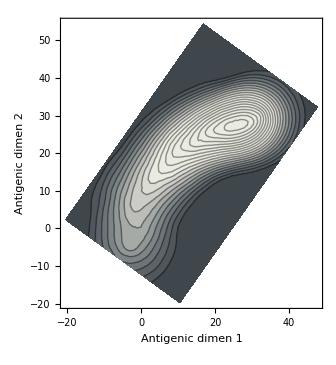

```mathematica
immunity=ListContourPlot[listLocs,Contours->Range[0.025, 0.975, 0.025], PlotRange->{Full,Full, Full}, AspectRatio->Automatic, ImageSize->336, FrameLabel->{"Antigenic dimen 1", "Antigenic dimen 2"}, ColorFunction->(ColorData["GrayTones"][(1-Rescale[#,{0.65,1}])+0.25] &), ColorFunctionScaling->False]
```

### Most recent with full population

```mathematica
viruses=Import["out.viruses","CSV"];
```

```mathematica
Length[viruses]
```

10283

```mathematica
viruses[[1;;3]]
```

{{43.6893,-8.7538},{44.172,-9.1053},{43.6498,-9.8622}}

```mathematica
plotRange={{37.5,52.5},{-3.5,-18.5}};
```

```mathematica
tallies=Tally[viruses];
```

```mathematica
tallies=Sort[tallies,#1[[2]]>#2[[2]]&];
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#[[1]]]]],Tooltip[Disk[#[[1]],N[Max[0.01*Sqrt[#[[2]]],0.07]]],#]}&,tallies];
```

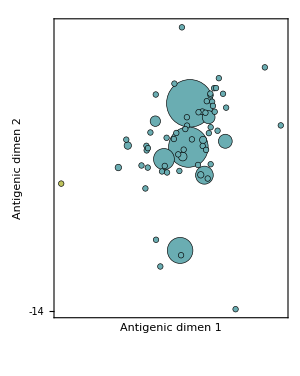

```mathematica
pop=Graphics[{EdgeForm[Thickness[0.0015]],Opacity[1],points},AspectRatio->Automatic,ImageSize->300,PlotRange->plotRange,FrameLabel->{"Antigenic dimen 1","Antigenic dimen 2"},Frame->{True,True,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,2}],None},{Table[{i,i,{0,0.005}},{i,-50,100,2}],None}},ImagePadding->fullPadding]
```

### Most recent with tree

Listing of child to parent relationships

```mathematica
endYear=40;
```

```mathematica
temp=branchData[[1001,1,1]]
```

36aff6d4

```mathematica
ancestorRules=Map[#[[1]]->#[[2]]&,branchData[[All,{1,2},1]]];
```

```mathematica
nodeList={};
```

```mathematica
gatherAncestors[id_]:=(nodeList=Join[nodeList,Drop[NestWhileList[#/.ancestorRules&,id,(#1≠#2&&FreeQ[nodeList,#])&,2],-1]])
```

```mathematica
gatherMultipleAncestors[list_]:=Union[Flatten[Map[gatherAncestors[#]&,list]]]
```

```mathematica
tipList=Select[tipData,#[[year]]>endYear-1&&#[[year]]≤endYear&][[All,1]];
```

```mathematica
gatherMultipleAncestors[tipList];
```

$Aborted

```mathematica
Length[nodeList]
```

9891

```mathematica
getThickness[count_]:=Thickness[Clip[0.002*N[Sqrt[count]],{0,0.01}]]
```

```mathematica
mutBranches=Select[branchData,(MemberQ[nodeList,#[[1,name]]]&&EuclideanDistance[#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]]>0.0000001&)];
```

```mathematica
firstLoc=rotate[{43.4,-12.5},0.95]
```

{35.4127,28.0312}

```mathematica
secondLoc=rotate[{43.650,-9.862},0.95]
```

{33.4124,29.769}

```mathematica
mutBranches2=Join[mutBranches,{{Join[{"1426241c",1,1,0,1,1,0},firstLoc],Join[{"6127c65c",1,1,0,1,1,369.9556},secondLoc],4}}];
```

```mathematica
branchLines=Map[{getThickness[#[[3]]],clusterColors[[clusterFunction[#[[1,{ag1,ag2}]]]]],Line[{#[[1,{ag1,ag2}]],Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}]}],clusterColors[[clusterFunction[#[[2,{ag1,ag2}]]]]],Line[{Mean[{#[[1,{ag1,ag2}]],#[[2,{ag1,ag2}]]}],#[[2,{ag1,ag2}]]}]}&,mutBranches];
```

```mathematica
branchLines={CapForm["Round"],branchLines};
```

```mathematica
mean=Mean[Select[tipData,(#[[year]]>endYear-1&&#[[year]]≤endYear)&][[All,{ag1,ag2}]]]
```

{32.6178,29.9836}

```mathematica
tallies=Tally[Select[tipData,(#[[year]]>endYear-1&&#[[year]]≤endYear)&][[All,{ag1,ag2}]]];
```

```mathematica
tallies=Tally[Join[Select[tipData,(#[[year]]>endYear-1&&#[[year]]≤endYear)&][[All,{ag1,ag2}]],Table[firstLoc,{7}]]];
```

```mathematica
tallies=Sort[tallies,#1[[2]]>#2[[2]]&];
```

```mathematica
points=Map[{clusterColors[[clusterFunction[#[[1]]]]],Disk[#[[1]],N[0.07*Sqrt[#[[2]]]]]}&,tallies];
```

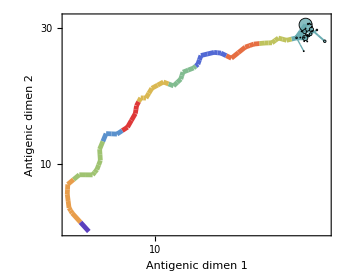

```mathematica
pop=Graphics[{EdgeForm[Thickness[0.0018]],branchLines,Opacity[0.8],points},AspectRatio->Automatic,ImageSize->72*4.8,PlotRange->All,FrameLabel->{"Antigenic dimen 1","Antigenic dimen 2"},Frame->{True,True,False,False},FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,5}],None},{Table[{i,i,{0,0.005}},{i,-50,50,5}],None}}]
```

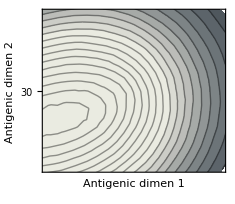

```mathematica
immunity=ListContourPlot[listLocs,Contours->Range[0.025, 0.975, 0.025], PlotRange->{{25,41},{23,37}, Full}, AspectRatio->Automatic, ImageSize->narrowWidth*0.925, FrameLabel->{"Antigenic dimen 1", "Antigenic dimen 2"}, ColorFunction->(ColorData["GrayTones"][(1-Rescale[#,{0.65,1}])+0.25] &), ColorFunctionScaling->False,FrameTicks->{{Table[{i,i,{0,0.005}},{i,-50,50,2}],None},{Table[{i,i,{0,0.005}},{i,-50,50,2}],None}}]
```

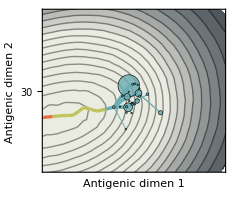

```mathematica
fig=Show[immunity,pop]
```

```mathematica
Export["immunityTree.pdf",fig,"PDF"]
```

immunityTree.pdf